#### Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, https://doi.org/10.1016/j.physrep.2017.12.001 [ arXiv:1610.06587v2] .

The reader should straightforwardly use this mathematica file to compute the total contribution of a generic model to the muon magnetic moment at 1-loop level. Plots are also available. We have closely followed the notation of our paper arxiv:

New Physics Contribution to (g-2)_μ

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
mμ=0.105; (*Muon mass*)
mν=0.1*10^-9; (*Neutrino mass*)
g=0.65;
SW2=0.231; SW=Sqrt[SW2]; CW=Sqrt[1-SW^2];(*Weinberg angle relations*)
ME=100; v=123;
C2W=CW^2-SW^2;
```

Experimental Bounds

based on (old): 

Current Bound: (295 ± 81) x 10^-11; 

Projected Bound:  (295 ± 34) x 10^-11; 

  

based on (new): 

Current Bound: (261 ± 78) x 10^-11; 

Projected Bound:  (261± 34) x 10^-11;

```mathematica
BoundProjectedup=Table[{x,295*10^-11},{x,1,10000,1}];
BoundProjecteddown=Table[{x,227*10^-11},{x,1,10000,1}];
BoundCurrenteup=Table[{x,339*10^-11},{x,1,10000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,10000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,10000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,10000,1}];
```

#### K^0+X^0 boson

```mathematica
MKX=√(g^2/2*(v^2+vqui^2));
mf9=ME; ϵ9=mf9/mμ;λ9=mμ/MKX;
gv9=g/(2*√2);
ga9=g/(2*√2);
ΔaKX=Table[{vqui,2*((gv9^2*mμ^2)/(8*π^2*MKX^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ9)+λ9^2*x^2*(1-ϵ9)^2*(1-x+ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MKX^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ9)+λ9^2*x^2*(1+ϵ9)^2*(1-x-ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}]) },{vqui,100,5000,50}];
```

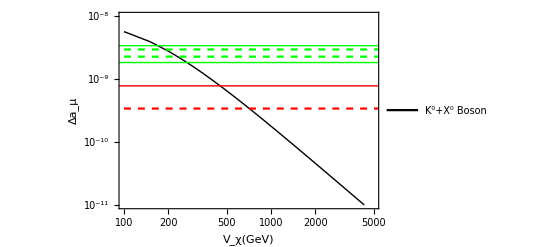

```mathematica
(* USe the commands below in case the Neutral Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

size9=Dimensions[ΔaKX];
ΔaKXnew=Table[{ΔaKX[[i,1]],-ΔaKX[[i,2]]},{i,1,size9[[1]]}];

(*Plot of the Neutral Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

ListLogLogPlot[{ΔaKXnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,5000},{10^-11,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"K^0+X^0 Boson"}],{0.5,0.9}]]
```

#### Z’ boson

```mathematica
(*Massa do bóson Z'*)
```

```mathematica
M={{a,b},{c,d}};
Eigenvalues[M]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
δ=√(SW^2/(4-6*SW^2));
a=g^2/CW^2*v^2;
b=g^2/CW^2*√2*δ*v^2*SW;
c=g^2/CW^2*√2*δ*v^2*SW;
d=g^2/CW^2*(2*δ^2)/SW^2*(v^2*(SW^4+CW^4)+vqui^2*CW^4);
```

```mathematica
MZp=√(a+d+√(a^2+4*b*c-2*a*d+d^2));
mf9=mμ; ϵ9=mf9/mμ;λ9=mμ/MZp;

gv9=g/(2*CW)*(0.5+SW^2)/(√(2-3*SW^2));
ga9=g/(2*CW)*C2W/(2*√(2-3*SW^2));
ΔaZp=Table[{vqui,1*((gv9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ9)+λ9^2*x^2*(1-ϵ9)^2*(1-x+ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ9)+λ9^2*x^2*(1+ϵ9)^2*(1-x-ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}]) },{vqui,100,5000,50}];
```

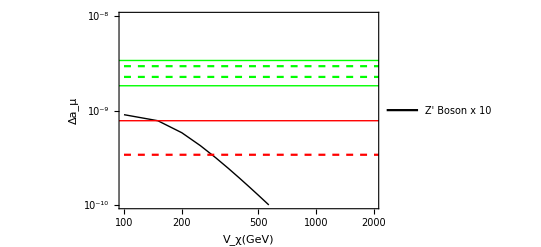

```mathematica
(* USe the commands below in case the Neutral Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

size9=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],ΔaZp[[i,2]]*10},{i,1,size9[[1]]}];

(*Plot of the Neutral Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

ListLogLogPlot[{ΔaZpnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{" Z' Boson x 10"}],{0.5,0.2}]]
```

COMBINED CONTRIBUTIONS

```mathematica
plottotal1=ListLogLogPlot[{ΔaZpnew,ΔaKXnew,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Purple,Thick],Directive[Black,Dashed],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{" Z' x 10 ","(K^0+X^0)x (-1)","Δa_μ Current","Δa_μ Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4\!\(\*SubscriptBox[\()\), \(L\)]\)⊗ U(1\!\(\*SubscriptBox[\()\), \(X\)]\) with Exotic leptons",12,Black, Bold]]
Export["/home/yoxara/Descargas/Figuras/341IndModelwithELME=100.pdf",plottotal1];
```

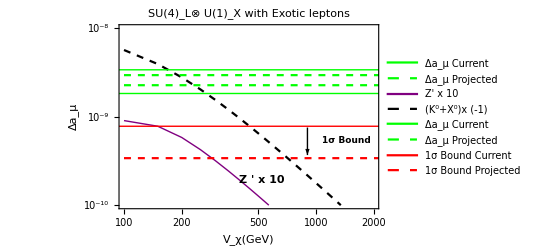

```mathematica
sizetotal=Dimensions[ΔaKX];
```

```mathematica
Totalcontri=Table[{ΔaZp[[i,1]],ΔaKX[[i,2]]+ΔaZp[[i,2]]},{i,1,sizetotal[[1]]}];
Totalcontrinew=Table[{Totalcontri[[i,1]],-Totalcontri[[i,2]]},{i,1,sizetotal[[1]]}];
```

```mathematica
plottotal10=ListLogLogPlot[{Totalcontrinew,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Total(-1)","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Current","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4\!\(\*SubscriptBox[\()\), \(L\)]\)⊗ U(1\!\(\*SubscriptBox[\()\), \(X\)]\) with Exotic leptons",12,Black, Bold]]
Export["/home/yoxara/Descargas/Figuras/341TotModelwithELME=100.pdf",plottotal10];
```